```mathematica
(*initialization cell: run once, and run again if changing variables*)
θ=.5;(*initial resistance*)
ϵ=1;(*random variable step size*)
α=.75;(*target*)
int=2; (*book calls this N, mathematical protects N*)
inttime=.5;(*time for intermediate sampling*)
duration=10000;(*time in seconds*)

test[p_]:=Boole[p-RandomReal[1]≥0];(*function that outputs 1 with probability p*)
zeta[prev_,t_]:=If[prev==0,test[t],test[t^2]];(*probability element for heartrate*)
indicator[x_]:=Boole[Round[(x/int)]==(x/int)];(*indicator if n is a natural number times int (book calls it N)*)
inter[t_]:=record[[Floor[(t/(int*inttime)) + 1]]];(*interpolation function*)
```

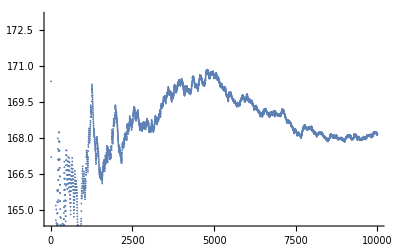

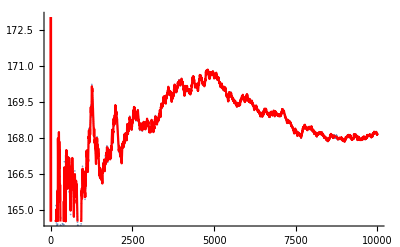

```mathematica
(*simulation step*)
pts=Floor[duration/(inttime*int)];
n=1;
record={θ};
temp=θ;
prev=0;
For[i=1,i≤pts,i++,
If[prev==0,draw=test[temp],draw=test[(temp)^2]];
prev=draw;
temp=temp-ϵ(Sum[draw-α,{i,n-int+1,n}])*indicator[n];
record=AppendTo[record,temp];
n+=1;
ϵ=1/n;
]
points=Table[{0+(i-1)*int*inttime,200*record[[i]]},{i,1,pts}];
ListPlot[points]
Show[ListPlot[points,PlotStyle->Opacity[.5]],Plot[200*inter[x],{x,0,duration},PlotStyle->Red]]
```